```mathematica
description="Slepton-side cirtual contribution";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
$ToolsRoot=ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
```

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)"; 
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
```

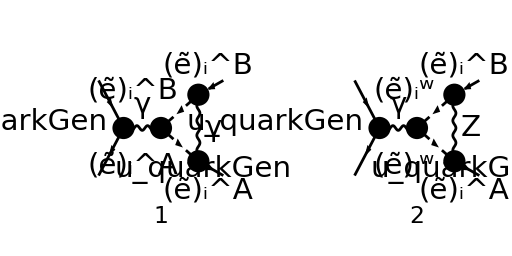

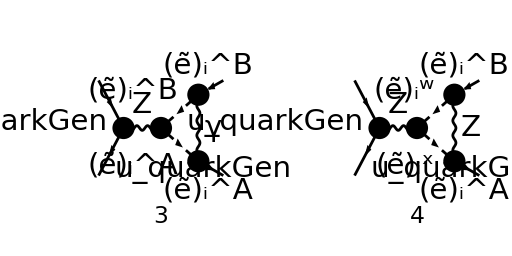

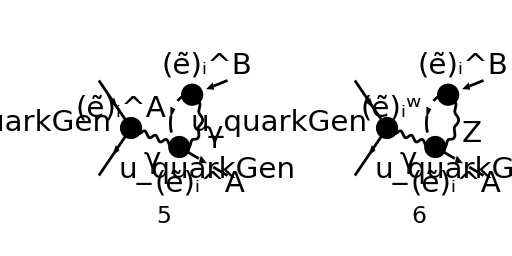

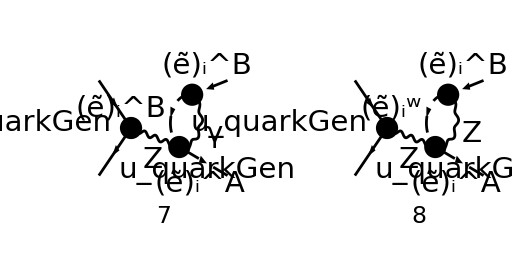

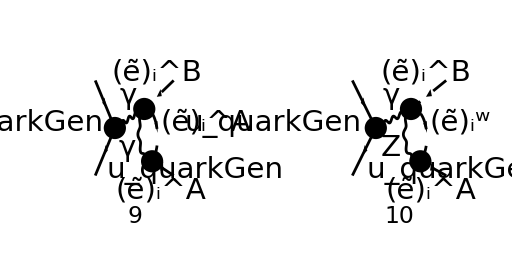

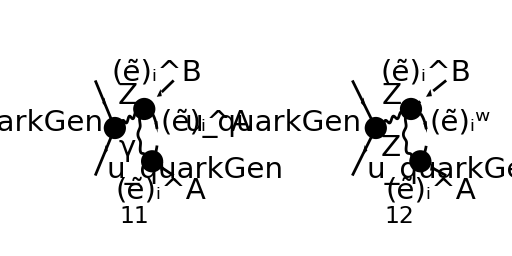

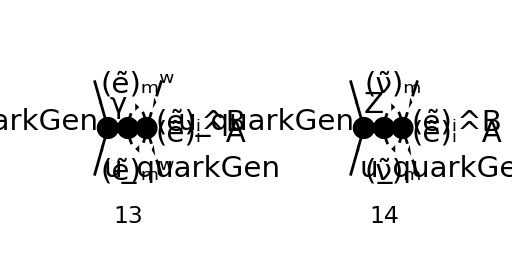

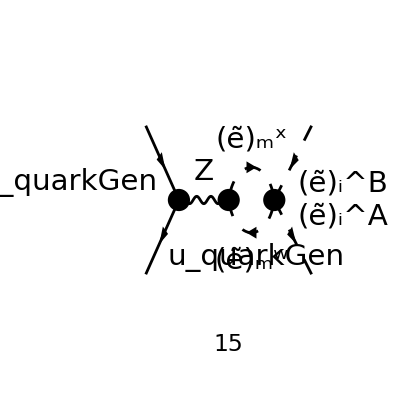

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{WFCorrections,Tadpoles, SelfEnergies}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1|2|3|4|5|6|13|14],F[3|4|11|12],V[3],U[1|2|3|4]}
(*
	S[1,...,6]=Higgs bosons,
	S[13,14]=squarks,
	F[3,4]=quarks (since we only want slepton-side corrections for now),
	F[11,12]=gauginos,
	V[3]=W boson,
	U[1,...,4]=ghosts,
*)
];
Paint[
diags[0],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

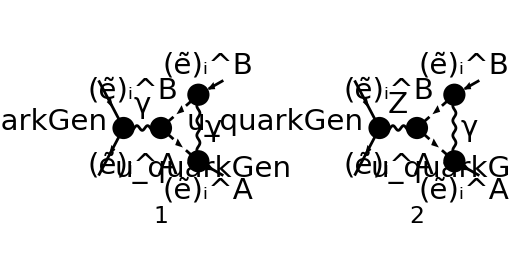

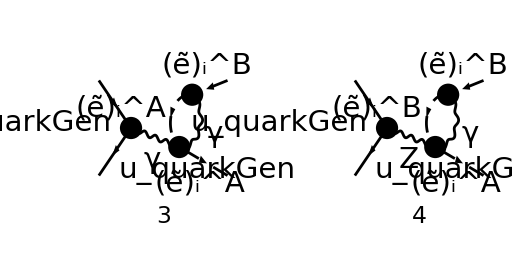

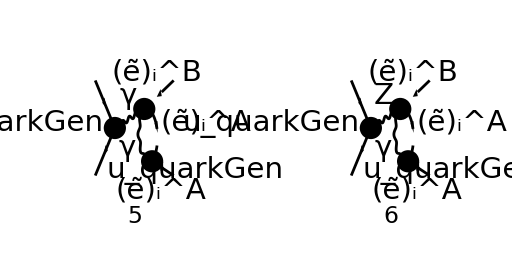

```mathematica
diags[1]=DiagramExtract[diags[0],{1,3,5,7,9,11}];
Paint[
diags[1],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{kloop},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
Contract->True,
DropSumOver->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{-((ⅈ (φ(-p_2)).(γ·(-k_1+k_2-2 kloop)).(φ(p_1)) IndexDelta(A,B) (4 (k_1·k_2)-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2) e^4 δ_Col1Col2)/(24 π^4 kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2) (k_1+k_2)^2)),-(((φ(-p_2)).((2 ⅈ (γ·(-k_1+k_2-2 kloop)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(-k_1+k_2-2 kloop)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (4 (k_1·k_2)-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(32 π^4 kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),-(ⅈ (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(12 π^4 (kloop^2-(MSf(A,2,i))^2).(k_1+kloop)^2 (k_1+k_2)^2),-(((φ(-p_2)).((2 ⅈ (γ·(kloop-k_1)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(kloop-k_1)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(16 π^4 (kloop^2-(MSf(B,2,i))^2).(k_1+kloop)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),(ⅈ (φ(-p_2)).(γ·(kloop-k_2)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(12 π^4 (kloop^2-(MSf(A,2,i))^2).(k_2+kloop)^2 (k_1+k_2)^2),((φ(-p_2)).((2 ⅈ (γ·(kloop-k_2)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(kloop-k_2)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(16 π^4 (kloop^2-(MSf(A,2,i))^2).(k_2+kloop)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))}

```mathematica
M1γ[0]=Mlist[0][[1]] 3/2 SMP["e_Q"]
```

-((ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2+4 (k_1·k_2)) (φ(-p_2)).(γ·(-2 kloop-k_1+k_2)).(φ(p_1)))/(16 π^4 (k_1+k_2)^2 kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2)))

```mathematica
M1Z[0]=Mlist[0][[2]]
```

-((e^3 (-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2+4 (k_1·k_2)) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(-2 kloop-k_1+k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·(-2 kloop-k_1+k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(32 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2)))

```mathematica
M1Z[1]=M1Z[0]//ZSimplify
```

(e^3 ZliAB (-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2+4 (k_1·k_2)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(-2 kloop-k_1+k_2)).(γ̄)^7+Zqr (γ·(-2 kloop-k_1+k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(16 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2))

```mathematica
M1Z[1]//DiracSubstitute67(*Easier to compare to hand calculations*)
```

(e^3 ZliAB (-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2+4 (k_1·k_2)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(-2 kloop-k_1+k_2)).(1/2-(γ̄)^5/2)+Zqr (γ·(-2 kloop-k_1+k_2)).((γ̄)^5/2+1/2)))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(16 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2))

```mathematica
M1[0]=M1γ[0]+M1Z[1]
```

(e^3 ZliAB (-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2+4 (k_1·k_2)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(-2 kloop-k_1+k_2)).(γ̄)^7+Zqr (γ·(-2 kloop-k_1+k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(16 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2))-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2+4 (k_1·k_2)) (φ(-p_2)).(γ·(-2 kloop-k_1+k_2)).(φ(p_1)))/(16 π^4 (k_1+k_2)^2 kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2))

```mathematica
M1[1]=M1[0]/.{Momentum[-k1+k2-2 kloop,D]->Momentum[-k1-2kloop+p1+p2-k1,D]}
```

(e^3 ZliAB (-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2+4 (k_1·k_2)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(-2 kloop-2 k_1+p_1+p_2)).(γ̄)^7+Zqr (γ·(-2 kloop-2 k_1+p_1+p_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(16 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2))-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2+4 (k_1·k_2)) (φ(-p_2)).(γ·(-2 kloop-2 k_1+p_1+p_2)).(φ(p_1)))/(16 π^4 (k_1+k_2)^2 kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((kloop-k_2)^2-(MSf(A,2,i))^2))

```mathematica
M1[2]=M1[1]//DiracSimplify//Simplify
```

(ⅈ e^4 δ_Col1Col2 (-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2+4 (k_1·k_2)) (-(2 ZliAB Zql (φ(-p_2)).(γ·kloop).(γ̄)^7.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)-(2 ZliAB Zqr (φ(-p_2)).(γ·kloop).(γ̄)^6.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)-(2 ZliAB Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)-(2 ZliAB Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)+(e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·kloop).(φ(p_1)))/(k_1+k_2)^2+(e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(k_1+k_2)^2))/(8 π^4 (cos(θ_W))^2 (sin(θ_W))^2 kloop^2.((k_1+kloop)^2-(MSf(B,2,i))^2).((k_2-kloop)^2-(MSf(A,2,i))^2))

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=0;
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M1[3]=M1[2]//TID[#,kloop,ToPaVe->True]&//FeynAmpDenominatorExplicit//DiracSimplify//Simplify
```

(e^4 (-4 ZliAB Zqr B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4-4 ZliAB Zqr B_0((MSf(B,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4-4 ZliAB Zql B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4-4 ZliAB Zql B_0((MSf(B,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4+2 ZliAB Zqr A_0((MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4+2 ZliAB Zql A_0((MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4+16 ZliAB Zqr C_0((MSf(A,2,i))^2,(MSf(B,2,i))^2,(MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^4 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4+16 ZliAB Zql C_0((MSf(A,2,i))^2,(MSf(B,2,i))^2,(MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^4 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4+8 ZliAB Zqr B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4-8 ZliAB Zqr B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4+8 ZliAB Zql B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4-8 ZliAB Zql B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^4+2 B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^4+2 B_0((MSf(B,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^4-A_0((MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^4-8 C_0((MSf(A,2,i))^2,(MSf(B,2,i))^2,(MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^4 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^4-4 B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^4+4 B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^4-2 ZliAB Zqr A_0((MSf(A,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-2 ZliAB Zql A_0((MSf(A,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-16 ZliAB Zqr C_0((MSf(A,2,i))^2,(MSf(B,2,i))^2,(MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^3 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-16 ZliAB Zql C_0((MSf(A,2,i))^2,(MSf(B,2,i))^2,(MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^3 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2+4 ZliAB Zqr B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2+12 ZliAB Zqr B_0((MSf(B,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-8 ZliAB Zqr B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2+4 ZliAB Zql B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2+12 ZliAB Zql B_0((MSf(B,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-8 ZliAB Zql B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-8 ZliAB Zqr B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2+8 ZliAB Zqr B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-8 ZliAB Zql B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2+8 ZliAB Zql B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-2 ZliAB Zqr A_0((MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-2 ZliAB Zql A_0((MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-8 ZliAB Zqr B_0((MSf(B,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^4 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2+8 ZliAB Zqr B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^4 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2-8 ZliAB Zql B_0((MSf(B,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^4 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2+8 ZliAB Zql B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^4 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 (MSf(A,2,i))^2+A_0((MSf(A,2,i))^2) (φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2+8 C_0((MSf(A,2,i))^2,(MSf(B,2,i))^2,(MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2)^3 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2-2 B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2-6 B_0((MSf(B,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2+4 B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2+4 B_0((MSf(A,2,i))^2,0,(MSf(A,2,i))^2) (φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2-4 B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2+A_0((MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2+4 B_0((MSf(B,2,i))^2,0,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^4 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2-4 B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^4 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2-2 B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^4 ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2-A_0((MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2+A_0((MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2-2 B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2) ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2 (MSf(A,2,i))^2+4 ZliAB Zqr B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (MSf(A,2,i))^2+4 ZliAB Zql B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^4 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (MSf(A,2,i))^2+2 ZliAB Zqr A_0((MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (MSf(A,2,i))^2-2 ZliAB Zqr A_0((MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (MSf(A,2,i))^2+2 ZliAB Zql A_0((MSf(A,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (MSf(A,2,i))^2-2 ZliAB Zql A_0((MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (MSf(A,2,i))^2+4 ZliAB Zqr B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (MSf(A,2,i))^2+4 ZliAB Zql B_0((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2),(MSf(A,2,i))^2,(MSf(B,2,i))^2) (φ(-p_2)).(γ·k_1+γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2) ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (MSf(A,2,i))^2+2 ZliAB Zqr A_0((MSf(A,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2+2 ZliAB Zql A_0((MSf(A,2,i))^2) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2-A_0((MSf(A,2,i))^2) (φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (MSf(B,2,i))^2 (k_1·k_2)^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2)) (cos(θ_W))^2 e_Q ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2) δ_Col1Col2)/(16 π^2 (MSf(A,2,i))^2 (MSf(B,2,i))^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k_1·k_2))^2 ((MSf(A,2,i))^2 (MSf(B,2,i))^2-(k_1·k_2)^2) (cos(θ_W))^2 ((MSf(A,2,i))^2+(MSf(B,2,i))^2-m_Z^2+2 (k_1·k_2)) (sin(θ_W))^2)